### 十阶内的数据

#### 获取数据

```mathematica
SimpleGraphs[n_]:=Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph"<>ToString@n<>".g6"];
Needs["IGraphM`"];
```

```mathematica
chkQ[n_,subgraph_]:=Module[{graphs,selected,m},
Print["time: ",Timing[
graphs=SimpleGraphs[n];
selected=Select[graphs,!IGSubisomorphicQ[subgraph,#]&];
m=(EdgeCount/@selected)//Max;
Print["Vertex number: ",n,"\nmaximal number of edges: ",m,"\ngraphs:"];
Print[Select[selected,EdgeCount@#==m&]];
""],"\n——————division line——————\n\n"]];
```

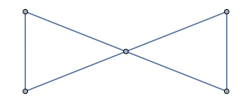

Vertex number: 5
maximal number of edges: 7
graphs:

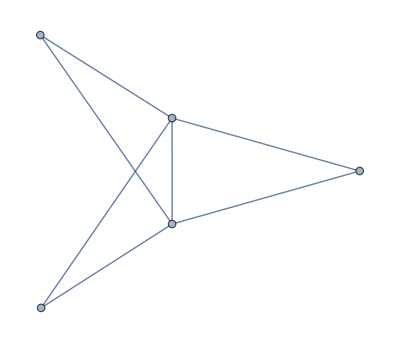
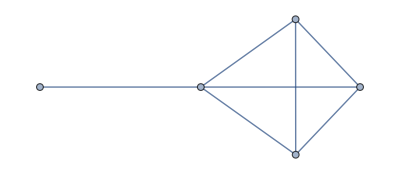
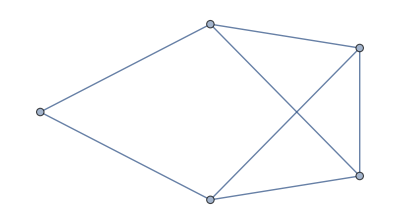

time: {0.119221,}
——————division line——————

Vertex number: 6
maximal number of edges: 10
graphs:

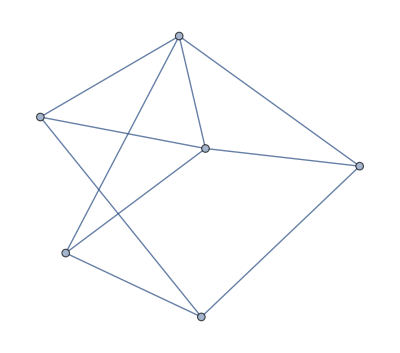

time: {0.253713,}
——————division line——————

Vertex number: 7
maximal number of edges: 13
graphs:

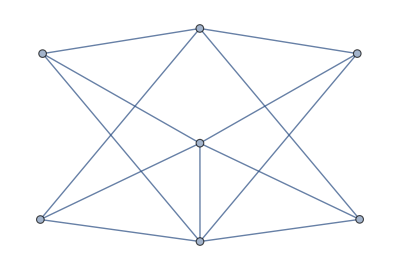
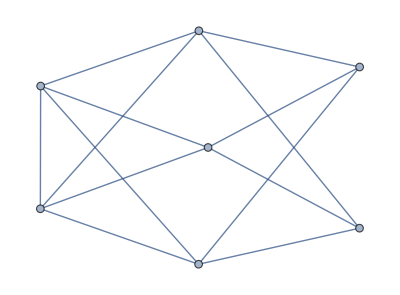

time: {0.902422,}
——————division line——————

Vertex number: 8
maximal number of edges: 17
graphs:

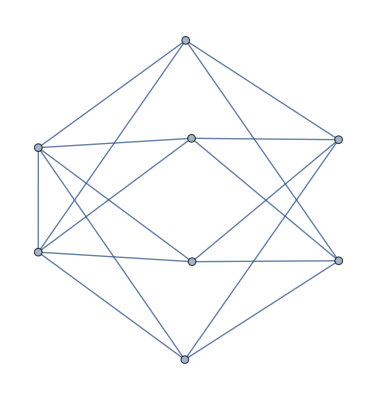

time: {3.54966,}
——————division line——————

Vertex number: 9
maximal number of edges: 21
graphs:

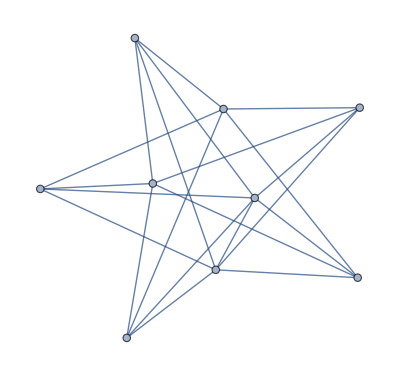
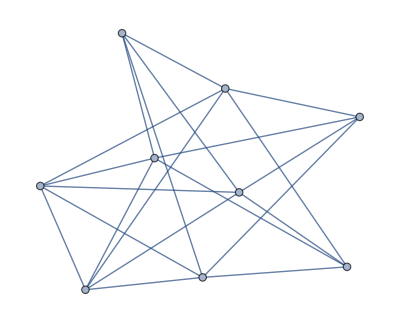

time: {80.3582,}
——————division line——————

```mathematica
subgraph=Graph[{1<->2,2<->3,1<->3,4<->5,4<->3,5<->3}]
chkQ[#,subgraph]&/@Range[5,10]
```